```mathematica
ClearAll["Global`*"]
```

```mathematica
(* For the prereheting scenario with inflaton potential , 
(1) we solve analytically the background (inflaton , Hubble ),the daughter mode function  and number density . While for the inflaton dynamics we consider the friction term , due to the expansion of the universe; in the spectator dynamics , we neglet the contribution from universe's expansion. *)
```

## Background equations for and

```mathematica
(* Background equations: EOM Inflaton field, Friedman equation *)
(*H[ϕ_,dϕ_]:=√((8π)/(3 Mpl^2)(1/2 dϕ^2 + 1/2 mϕ^2 ϕ^2+ λ/4 ϕ^4));*)
H[ϕ_,dϕ_]:=√((8π)/(3 Mpl^2)(1/2 dϕ^2 + 1/2 mϕ^2 ϕ^2));
eqa = a'[t]==a[t]*H[ϕ[t],ϕ'[t]];
(*eqϕ=ϕ''[t]+3H[ϕ[t],ϕ'[t]]ϕ'[t]+mϕ^2 ϕ[t]+λ ϕ[t]^3==0;*)
eqϕ=ϕ''[t]+3H[ϕ[t],ϕ'[t]]ϕ'[t]+mϕ^2 ϕ[t]==0;

(*Initial conditions*)
backgroundconditions = {a[0]==1,ϕ[0]==Φ,ϕ'[0]==0};

(* Solve Background dynamic *)
solbackground=DSolve[{eqϕ,eqa,backgroundconditions[[1]],backgroundconditions[[2]],backgroundconditions[[3]]},{ϕ[t],a[t]},t];

(* Solution's background *)
ϕsol[t_]:=Simplify[ϕ[t]/. solbackground[[1]]];
asol[t_]:=Simplify[a[t]/. solbackground[[1]]];
Hsol[t_]:=H[ϕsol[t],D[ϕsol,t]];
```

## Daughter dynamic:

```mathematica
(* Frequency *)
ω2[t_]:=k^2+g^2 ϕsol[t]^2;
ω[t_]:=√ω2[t];

(* EOM daughter χ *)
eqχ=χ''[t]+ω2[t]*χ[t]==0;

(*Initial conditions*)
χconditions={χ[0]==1/(√(2ω[0])),χ'[0]==-I*√(ω[0]/2)}; (* Initial conditions  to be valued at  *)

(*Solve χ dynamic *)
solχ=DSolve[{eqχ,χconditions[[1]],χconditions[[2]]},χ[t],t];

(* Spectator solution *)
χsol[t_]=Simplify[χ[t] /. solχ[[1]]];

(* Number particles *)
numbχ[t_]=1/2 Abs[χsol'[t]]^2/ω[t]+ω[t]/2 Abs[χsol[t]]^2-1/2 //Simplify;
```

## Specific momenta

```mathematica
Mpl=1;                    (* reduced mass Planck *)
mϕ=1;                      (* inflation mass *)
λ = 0;                       (* self-coupling constant *)
g=200;                    (* coupling constant ϕ-χ *)
tMax=50;               (* time *)
Φ=1/10 Mpl;                (* initial amplitude ϕ *)
```

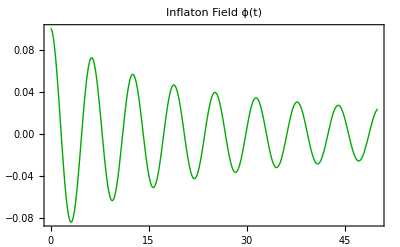

```mathematica
(*Plots *)
aHPlot = Plot[{asol[t],Hsol[t]},{t,0,tMax},PlotRange->All,PlotLegends->{"a(t)","H(t)"},Frame->True,PlotLabel->"Scale factor and Hubble evolution"];
ϕPlot = Plot[ϕsol[t],{t,0,tMax},PlotRange->All,PlotStyle->{Thick,Darker[Green]},Frame->True,PlotLabel->"Inflaton Field ϕ(t)"];
GraphicsGrid[Partition[{aHPlot,ϕPlot},2,2,{1,2},""]]
```

```mathematica
Manipulate[Plot[Re[solχ[k][t]],{t,0,tMax},PlotRange->All,AxesLabel->Automatic,PlotStyle->{Thick,Darker[Blue]},PlotLabel->Style[StringForm["Spectator Field χ_k(z) for different modes k"],14]],{k,0.1,3.0}]

Manipulate[Plot[numberχ[z,k],{z,0,tMax},PlotRange->All,AxesLabel->Automatic,PlotStyle->{Thick,Darker[Blue]},PlotLabel->Style[StringForm["Number density n_k(z) for different modes k"],14]],{k,0.1,3.0}]
```